# Polymer Assembly & Disassembly

## Supporting Information Insights into chemically-fueled supramolecular polymers

Anastasiia Sharko, Dimitri Livitz, Serena De Piccoli1, Kyle J. M. Bishop, and Thomas M. Hermans

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
```

## Isodesmic Polymerization Model

### Equilibrium Distribution

UNITS: All concentrations are scaled by the dissociation constant K.

#### Free monomer concentration a_1 vs total monomer concentration m_1

Equation (1.13)

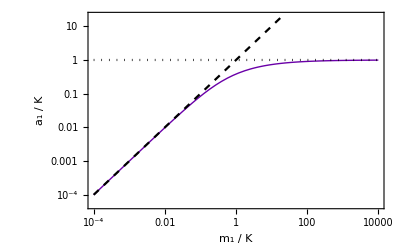

```mathematica
Clear[m1]
LogLogPlot[{
1/(2 m1)(1+2 m1- √(1+4 m1)),
m1,
1},{m1,10^-4,10^4},
PlotStyle->{Directive[Thick,MPLColorMap["Plasma"][0.2]],
Directive[Dashed,Black],
Directive[Dotted, Black]},
Frame->True,
PlotRange->{5 10^-5,2 10},
LabelStyle->Directive[Black,FontSize->12],
FrameLabel->{"m_1 / K","a_1 / K"}]
```

#### Polymer size distribution

Equation (1.11)

```mathematica
Manipulate[
DiscretePlot[(1/(2 m1)(1+2 m1- √(1+4 m1)))^n/.m1->10^logm1,{n,1,100},
PlotRange->{0,1.05},
Frame->True,
PlotStyle->MPLColorMap["Plasma"][0.2],
PlotRange->{5 10^-5,2 10},
PlotLabel->Style[StringForm["m_1/K = ``",NumberForm[10^logm1,4]]],
LabelStyle->Directive[Black,FontSize->12],
FrameLabel->{"polymer size, n","a_n / K"}],{{logm1,2},-1,3}]
```

### Polymerization Kinetics

UNITS: Time is scaled by k_-^-1 and concentrations by  k_-/k_+=K.

#### Moment Evolution Equations (1.21)

Specify the parameters:

	length,L=m_1/m_0=(2 m_1)/(K(-1+√(1+4 m_1/K))
	m_1/K=L(L-1)

```mathematica
L=5; (* average equilibrium length, Subscript[m, 1]/Subscript[m, 0] *)
tmax = 2; (* time to integrate *)
m1=L(L-1); (* total monomer concentration *)
m0∞=1/2(-1+Sqrt[1+4 m1]); (* asymptotic 0th moment *)
m2∞=m1 Sqrt[1+4 m1];  (* asymptotic 2nd moment *)
```

Integrate the moment equations.

```mathematica
Clear[m0,m2]
solm=NDSolve[{
m0'[t]==-m0[t]^2+(m1-m0[t]),
m2'[t]==2 m1^2+2m1(m1/m0[t]-(m1/m0[t])^2),
m0[0]==m1,
m2[0]==m1},{m0[t],m2[t]},{t,0,tmax}];
```

0th moment m_0(t)

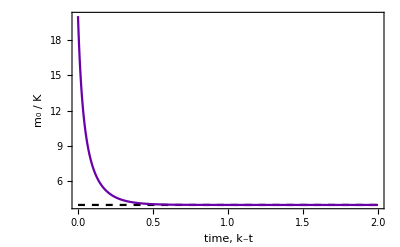

```mathematica
Plot[{m0∞,m0[t]/.solm[[1]]},{t,0,tmax},
PlotRange->Full,
Frame->True,
PlotStyle->{Directive[Black,Dashed],MPLColorMap["Plasma"][0.2]},
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, k_-t"],Style["m_0 / K"]}]
```

2nd moment m_2(t)

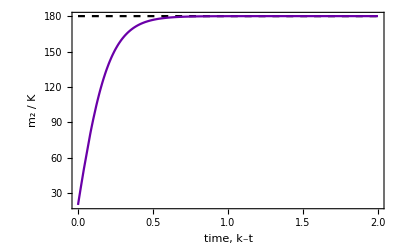

```mathematica
Plot[{m2∞,m2[t]/.solm[[1]]},{t,0,tmax},
PlotRange->Full,
Frame->True,
PlotStyle->{Directive[Black,Dashed],MPLColorMap["Plasma"][0.2]},
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, k_-t"],Style["m_2 / K"]}]
```

dispersity

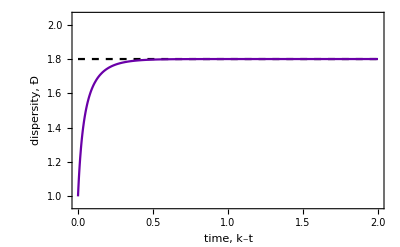

```mathematica
Plot[{(2m1 - m0∞)/m1,(2m1 - m0[t])/m1/.solm[[1]]},{t,0,tmax},
PlotRange->{0.95,2.05},
Frame->True,
PlotStyle->{Directive[Black,Dashed],MPLColorMap["Plasma"][0.2]},
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, k_-t"],Style["dispersity, Ð"]}]
```

#### Polymer Size Distribution

Specify the parameters:

```mathematica
nmax=100; (* maximum polymer size, should be several times the equilibrium length *)
```

Integrate numerically equation 1.18

	(ȧ)_n=-2 k_+a_n(∑_(j=1)^∞ a_j)+k_+∑_(j=1)^(n-1) a_j a_(n-j)-k_-(n-1)a_n+2 k_-∑_(j=1)^∞ a_(n+j)

```mathematica
Clear[a]
nn=Table[n,{n,1,nmax}];
aa[t_]=Table[Subscript[a,n][t],{n,1,nmax}];
aa0=Table[m1 KroneckerDelta[1,n],{n,1,nmax}];

(* governing equations *)
rhs=Table[
-2  Subscript[a, n][t] Sum[Subscript[a, j][t],{j,1,nmax}]
+  Sum[Subscript[a, j][t]Subscript[a, n-j][t],{j,1,n-1}]
-(n-1)Subscript[a, n][t]
+2 Sum[Subscript[a, n+j][t],{j,1,nmax-n}],
{n,1,nmax}];
eqns=Thread[D[aa[t],t]==rhs];

(* initial conditions *)
initc=Flatten[{Thread[aa[0]==aa0]}];

(* solution *)
sol=NDSolve[{eqns,initc},aa[t],{t,0,tmax}];
```

Visualize solution

```mathematica
Manipulate[
Show[
ListPlot[ aa[t]/.sol[[1]]/.t->time,
Frame->True,
Joined->False,
PlotStyle->{Thin,MPLColorMap["Plasma"][0.2]},
PlotMarkers->{•},
PlotRange->{-0.05 ,1.6}(1/(2 m1)(1+2 m1- √(1+4 m1))),
LabelStyle->{FontSize->12,Black},
PlotLabel->Style[StringForm["time = `` k_-^-1",NumberForm[time,4]]],FrameLabel->{Style["polymer size, n"],Style["concentration a_n / K"]}],
Plot[m0[t]^2/m1(1- m0[t]/m1)^(n-1)/.solm[[1]]/.t->time,{n,1,nmax},
PlotRange->Full,PlotStyle->Directive[MPLColorMap["Plasma"][0.4]]]],
{{time,0.1},0,tmax}]
```

Check monomer conservation.

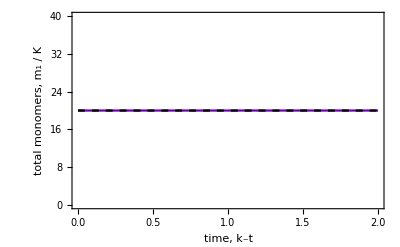

```mathematica
Plot[{Total[nn aa[t]]/.sol[[1]],m1},{t,0,tmax},
PlotRange->{0,2 m1},
Frame->True,
PlotStyle->{MPLColorMap["Plasma"][0.2],Directive[Black,Dashed]},
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, k_-t"],Style["total monomers, m_1 / K"]}]
```

Compare to predictions of the moment equations.

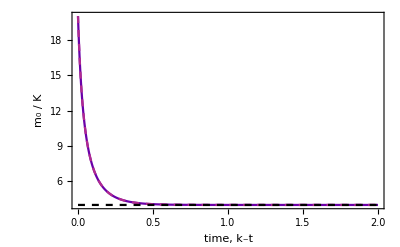

```mathematica
Plot[{Total[ aa[t]]/.sol[[1]],m0[t]/.solm[[1]],m0∞},{t,0,tmax},
PlotRange->Full,
Frame->True,
PlotStyle->{MPLColorMap["Plasma"][0.2],Directive[MPLColorMap["Plasma"][0.4],Dashed],Directive[Black,Dashed]},
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, k_-t"],Style["m_0 / K"]}]
```

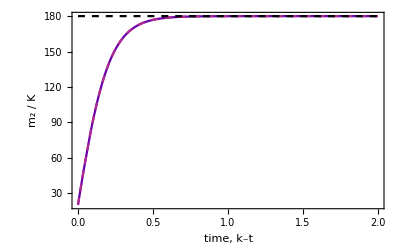

```mathematica
Plot[{Total[ nn^2 aa[t]]/.sol[[1]],m2[t]/.solm[[1]],m2∞},{t,0,tmax},
PlotRange->Full,
Frame->True,
PlotStyle->{MPLColorMap["Plasma"][0.2],Directive[MPLColorMap["Plasma"][0.4],Dashed],Directive[Black,Dashed]},
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, k_-t"],Style["m_2 / K"]}]
```

Supporting Figure 1

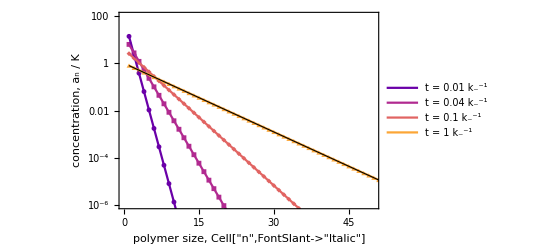

```mathematica
bigSize = 14;
smallSize=12;
thin =0.6;
distPlot=Show[ListLogPlot[ {
aa[t]/.sol[[1]]/.t->0.01,
aa[t]/.sol[[1]]/.t->0.04,
aa[t]/.sol[[1]]/.t->0.1,
aa[t]/.sol[[1]]/.t->1},
Frame->True,
PlotStyle->{MPLColorMap["Plasma"][0.2],MPLColorMap["Plasma"][0.4],MPLColorMap["Plasma"][0.6],MPLColorMap["Plasma"][0.8]},
PlotMarkers->{Automatic,Offset[5]},
PlotRange->{{0,50},{10^-6,10^2}},
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{
Style["polymer size, Cell["n",FontSlant->"Italic",ExpressionUUID->"5249d92f-7370-49cb-8010-cf72192c019e"]",FontSize->bigSize],
Style["concentration, a_n / K",FontSize->bigSize]}],
LogPlot[{
m0[t]^2/m1(1- m0[t]/m1)^(n-1)/.solm[[1]]/.t->0.01,
m0[t]^2/m1(1- m0[t]/m1)^(n-1)/.solm[[1]]/.t->0.04,
m0[t]^2/m1(1- m0[t]/m1)^(n-1)/.solm[[1]]/.t->0.1,
m0[t]^2/m1(1- m0[t]/m1)^(n-1)/.solm[[1]]/.t->1,
(m0∞)^2/m1(1- (m0∞)/m1)^(n-1)},{n,1,nmax},
PlotRange->Full,
PlotLegends->Placed[{
Style["t = 0.01 k_-^-1",FontSize->smallSize],
Style["t = 0.04 k_-^-1",FontSize->smallSize],
Style["t = 0.1 k_-^-1",FontSize->smallSize],
Style["t = 1 k_-^-1",FontSize->smallSize]},{0.8,0.7}],
PlotStyle->{MPLColorMap["Plasma"][0.2],MPLColorMap["Plasma"][0.4],MPLColorMap["Plasma"][0.6],MPLColorMap["Plasma"][0.8],Directive[Black,AbsoluteThickness[0.8]]}]]
```

```mathematica
(* Export[NotebookDirectory[]<>"polymer_kinetics.pdf",distPlot] *)
```

## Cooperative Polymerization Model

### Equilibrium Distribution

```mathematica
μ[n_]=1/2 ((n-nc) ε+(-2+n+nc) εc+(ε-εc) Abs[n-nc]); (* chemical potential, Subscript[μ, n] *)
lnKij=FullSimplify[μ[i+j]-μ[i]-μ[j]] (* equilibrium constant, Subscript[K, ij]*)
```

1/2 nc (ε-εc)+εc-1/2 (ε-εc) (Abs[i-nc]+Abs[j-nc]-Abs[i+j-nc])

Supplemental Figure 2

```mathematica
param={min->0.1,max->0.7,nc->4};
Kijplot=Show[
ContourPlot[lnKij/.{ε->-(max-min-max nc)/nc,εc->max}/.param,{j,0.9,7.1},{i,0.9,7.1},
Contours->10,
MaxRecursion->2,
PlotRange->{{0.9,7.1},{0.9,7.1}},
PlotPoints->50,
ColorFunctionScaling->False,
ColorFunction->MPLColorMap["Plasma"],
ImageSize->350,
ImagePadding->{{40,20},{40,20}},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{
Style["i",FontSize->bigSize],
Style["j",FontSize->bigSize]},
LabelStyle->Directive[Black,FontSize->smallSize]],
Graphics[{GrayLevel[0.9],Dashed,AbsoluteThickness[1],Line[{{0,4},{8,4}}],Line[{{4,0},{4,8}}],Line[{{0,4},{4,0}}]/.param}],
ListPlot[Table[{i,j},{i,1,7},{j,1,7}],PlotStyle->{GrayLevel[0.9]}]];
```

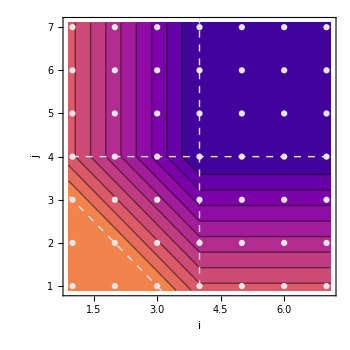

```mathematica
Kijplot2=Graphics[{Inset[Kijplot],
Text[Style["coagulation",FontSize->bigSize,White],Scaled[{0.73,0.74}]],
Text[Style["elongation",FontSize->bigSize,White],Scaled[{0.34,0.74}]],
Text[Style["elongation",FontSize->bigSize,White],Scaled[{0.73,0.34}]],
Text[Style["nucleation",FontSize->bigSize,White],Scaled[{0.37,0.37}],
Automatic, {1,-1}],
Text[Style["clustering",FontSize->bigSize,White],Scaled[{0.23,0.23}],Automatic, {1,-1}],
Text[Style["subcritical",FontSize->bigSize,Black],Scaled[{0.34,1}]],
Text[Style["supercritical",FontSize->bigSize,Black],Scaled[{0.73,1}]]}]
```

```mathematica
(*Export[NotebookDirectory[]<>"Kijplot_plot.pdf",Kijplot2]*)
```

Supplemental Figure 3a
Equation (1.27)

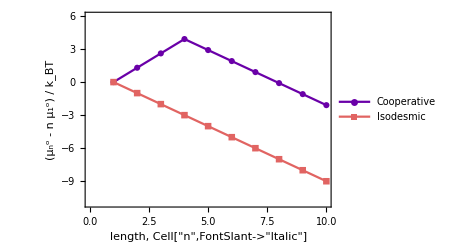

```mathematica
energyPlot=DiscretePlot[{
μ[n]/.{ε->-1,nc->4,εc->Log[10]-1},
(n-1) ε/.{ε->-1}},{n,1,10}, Filling->None,Joined->True,PlotMarkers->Automatic,
Frame->True,
AspectRatio->3.5/5,
PlotRange->{{0,10},{-11,6}},
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
PlotStyle->{MPLColorMap["Plasma"][0.2],MPLColorMap["Plasma"][0.6]},
LabelStyle->{FontSize->smallSize,Black},
PlotLegends->Placed[{"Cooperative","Isodesmic"},{0.22,0.2}],
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{Style["length, Cell["n",FontSlant->"Italic",ExpressionUUID->"0d4fae4a-2ae1-4352-b17b-951c51d8e28b"]",FontSize->bigSize],Style["(μ_n^o - n μ_1^o) / k_BT",FontSize->bigSize]}]
```

Supplemental Figure 3b
Equation (1.30)

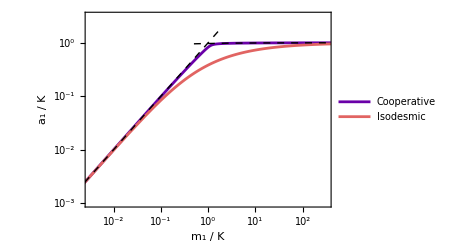

```mathematica
Clear[m1]
m1=a1^(nc+1)/Kc^(nc-1)((nc a1 -(nc+1)Kc)/(a1-Kc)^2-(nc a1 -(nc+1)Kd)/(a1-Kd)^2)+(a1 Kc^2)/(a1-Kc)^2;
param={nc->4,Kc->10,Kd->1};

coopPlot=Show[
ParametricPlot[{
{Log10[m1/.param],Log10[a1]},
{Log10[m1/.{Kc->1,Kd->1,nc->1}],Log10[a1]}},{a1,10^-3,1},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[2]],Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[2]]},
AspectRatio->3.5/5,
FrameTicks->{
{Table[{i,Superscript[10,i]},{i,-3,2,1}],
Table[{i,""},{i,-3,2,1}]},
{Table[{i,Superscript[10,i]},{i,-2,2,1}],
Table[{i,""},{i,-2,2,1}]}},
Frame->True,
Axes->False,
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{
Style["m_1 / K",FontSize->bigSize],
Style["a_1 / K",FontSize->bigSize]},
PlotRange->{{-2.5,2.5},{-3,0.5}},
LabelStyle->Directive[Black,FontSize->smallSize],
PlotLegends->Placed[{"Cooperative","Isodesmic"},{0.78,0.2}]],
Plot[Log10[Kd-Kd √((Kd/10^logm1)(Kd/Kc)^(nc-1))]/.param,{logm1,-0.3,3},
PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1]]],
Plot[logm1,{logm1,-3,0.3},
PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1]]]]
```

```mathematica
grid=Style[Grid[{{
Graphics[{Inset[energyPlot],
Text[Style["a",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
AspectRatio->3.5/5],
Graphics[{Inset[coopPlot],
Text[Style["b",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
AspectRatio->3.5/5],}}],ImageSizeMultipliers->{1,1}]
```

-Graphics- | -Graphics- |

```mathematica
(* Export[NotebookDirectory[]<>"cooperative_equilibrium.pdf",grid] *)
```

Visualize distribution.

```mathematica
sola=FindRoot[(m1/.param)==100,{a1,0.988}]
```

{a1→0.996823}

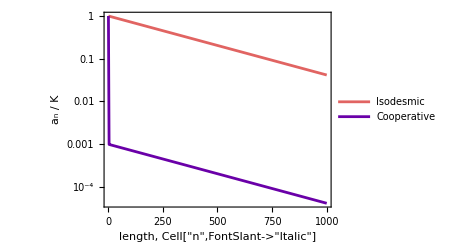

```mathematica
LogPlot[{(a1/.sola[[1]])^n Exp[-μ[n]]/.{ε->Log[1],εc->Log[1],nc->1}/.param,
(a1/.sola[[1]])^n Exp[-μ[n]]/.{ε->Log[Kd],εc->Log[Kc]}/.param},{n,1,1000}, Filling->None,
Frame->True,
PlotRange->Full,
AspectRatio->3.5/5,
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[2]],Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[2]]},
LabelStyle->{FontSize->smallSize,Black},
PlotLegends->Placed[{"Isodesmic","Cooperative"},{0.8,0.4}],
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{Style["length, Cell["n",FontSlant->"Italic",ExpressionUUID->"9786aded-1ba2-497e-86a6-813c3599e404"]",FontSize->bigSize],Style["a_n / K",FontSize->bigSize]}]
```

### Polymerization Kinetics

UNITS: All concentrations are scaled by the dissociation constant K=e^ε; time by k_+^-1.

Specify parameters:

```mathematica
Kc=10; (* equilibrium dissociation constant,  Subscript[K, c]=e^Subscript[ε, c] *)
nc=4; (* critical nucleus size *)
m1=10;(* total monomer concentration *)
tmax = 200; (* maximum time *)
nmax=500;  (* maximum polymer size *)

ε=Log[1];
εc=Log[Kc];
kn[i_,j_]:= Exp[2 (ε-εc)+εc-1/2 (ε-εc) (Abs[-4+i]+Abs[-4+j]-Abs[-4+i+j])]
```

Compute equilibrium distribution.

```mathematica
L=Sqrt[m1/Kd(Kc/Kd)^(nc-1)] (* approximate polymer length *)
 a1eq=a1/.FindRoot[a1^(nc+1)/Kc^(nc-1)((nc a1 -(nc+1)Kc)/(a1-Kc)^2-(nc a1 -(nc+1))/(a1-1)^2)+(a1 Kc^2)/(a1-Kc)^2==m1,{a1,0.8,0,0.9999999999 ⅇ^-ε}];
L=1/-Log[a1eq] (* exact polymer length *)
```

100

93.7641

Numerical solution of equations (1.33)

```mathematica
nn =Table[n,{n,1,nmax}];
aa0=Table[m1 KroneckerDelta[1,n],{n,1,nmax}];
aa[t_]=Table[Subscript[a,n][t],{n,1,nmax}];

(* governing equations *)
rhs=Flatten[{
(* Subscript[ȧ, n] *)
Table[
-2 Subscript[a, n][t] Sum[Subscript[a, j][t],{j,1,nmax-n}]
+ Sum[Subscript[a, n-j][t]Subscript[a, j][t],{j,1,n-1}]
-Subscript[a, n][t] Sum[kn[n-j,j],{j,1,n-1}]
+2  Sum[kn[n,j]Subscript[a, n+j][t],{j,1,nmax-n}],
{n,1,nmax}]}];

eqns=Thread[
Flatten[{D[aa[t],t]}]==rhs];

(* initial conditions *)
initc=Flatten[{Thread[aa[0]==aa0]}];

(* solution *)
sol=NDSolve[{eqns,initc},aa[t],{t,0,tmax},
Method->{"EquationSimplification"->"Residual"}];
```

Check monomer conservation.

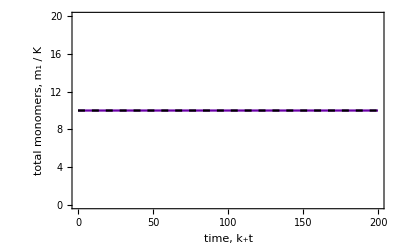

```mathematica
Plot[{Total[nn aa[t]]/.sol[[1]],m1},{t,0,tmax},
PlotRange->{0,2 m1},
Frame->True,
PlotStyle->{MPLColorMap["Plasma"][0.2],Directive[Black,Dashed]},
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, k_+t"],Style["total monomers, m_1 / K"]}]
```

Polymer Distributions.

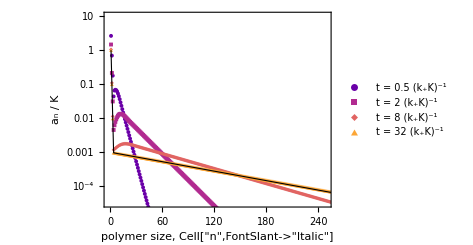

```mathematica
distPlot=Show[
ListLogPlot[{ aa[t]/.sol[[1]]/.t->0.5, 
aa[t]/.sol[[1]]/.t->2,
aa[t]/.sol[[1]]/.t->8,
aa[t]/.sol[[1]]/.t->32},
Frame->True,
ImageSize->350,
AspectRatio->3.5/5,
ImagePadding->{{60,20},{60,20}},
PlotMarkers->{Automatic,Offset[4]},
PlotStyle->{
Directive[Thin,MPLColorMap["Plasma"][0.2]],
Directive[Thin,MPLColorMap["Plasma"][0.4]],
Directive[Thin,MPLColorMap["Plasma"][0.6]],Directive[Thin,MPLColorMap["Plasma"][0.8]]},
PlotLegends->Placed[{
Style["t = 0.5 (k_+K)^-1",FontSize->smallSize],
Style["t = 2 (k_+K)^-1",FontSize->smallSize],
Style["t = 8 (k_+K)^-1",FontSize->smallSize],
Style["t = 32 (k_+K)^-1",FontSize->smallSize]},{0.8,0.7}],
PlotRange->{{-2,nmax/2},{10^-4.5,10}},
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{
Style["polymer size, Cell["n",FontSlant->"Italic",ExpressionUUID->"cab5f957-12cf-4d24-9c28-982da84adf94"]",FontSize->bigSize],
Style["a_n / K",FontSize->bigSize]}],
LogPlot[ a1eq^n Exp[-μ[n]],{n,1,nmax},PlotRange->Full,PlotStyle->Directive[AbsoluteThickness[0.8],Black,Opacity[1]]]]
```

Extent of polymerization.

Here, we include all subcritical polymers P_(n≤n_c) in our count of free monomers.

```mathematica
α=(m1-Sum[n Subscript[a, n][t]/.sol[[1]],{n,1,nc}])/m1;
αeq=Sum[n a1eq^n Exp[-μ[n]],{n,nc,Infinity}]/m1;
```

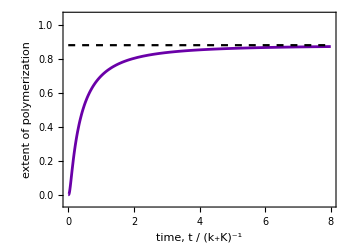

```mathematica
extent=Plot[{α,αeq},{t,0,8},
Frame->True,
PlotRange->{-0.05,1.05},
ImageSize->350,
AspectRatio->3.5/5,
ImagePadding->{{60,20},{60,20}},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[2]],Directive[Black,Dashed],
Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[2],Opacity[0.2]]},
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{
Style["time, t / (k_+K)^-1",FontSize->bigSize],Style["extent of polymerization",FontSize->bigSize]}]
```

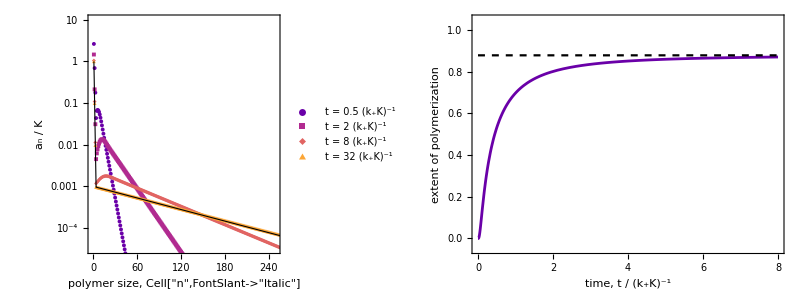

```mathematica
grid=Style[Grid[{{
Graphics[{Inset[distPlot],
Text[Style["a",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
AspectRatio->3.5/5],
Graphics[{Inset[extent],
Text[Style["b",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
AspectRatio->3.5/5]}}],ImageSizeMultipliers->{1,1}]
```

```mathematica
(*Export[NotebookDirectory[]<>"coop_kinetics.pdf",grid] *)
```

Animation (may take a minute...)

```mathematica
plots=Table[Show[ListPlot[ nn aa[t]/.sol[[1]]/.t->time,
Frame->True,
Joined->True,
PlotStyle->{Thin,MPLColorMap["Plasma"][0.2]},
PlotMarkers->{•},
AspectRatio->3.5/5,
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
PlotRange->{{-5,nmax},{0,0.2}},
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{Style["length, n",FontSize->bigSize],Style["n a_n / K",FontSize->bigSize]},
Epilog->Inset[Style[StringForm["t / (k_+K)^-1 = ``",NumberForm[N[time,1],{3,1}]],FontSize->bigSize],Scaled[{0.55,0.85}],{Left,Center}]],
Plot[ n a1eq^n Exp[-μ[n]],{n,1,nmax},
PlotRange->Full,
PlotStyle->Directive[Thick,MPLColorMap["Plasma"][0.2],Opacity[0.3]]]],{time,0,25,0.2}];
```

```mathematica
ListAnimate[plots]
```

fmpeg -i polymer_distribution.gif -movflags faststart -pix_fmt yuv420p -vf “scale=trunc(iw/2)*2:trunc(ih/2)*2” polymer_distribution.mp4

```mathematica
(*Export[NotebookDirectory[]<>"polymer_distribution.gif",plots,ImageResolution->350,"AnimationRepetitions"->∞]*)
```